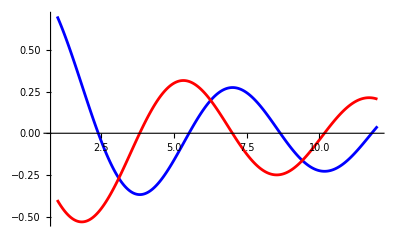

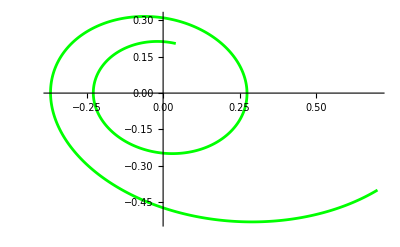

```mathematica
f[x_,y_]:=x*y;
fx[y_]:=y;
fy[t_,x_,y_]:=-y/t-x;

(*Метод Эйлера для систем*)
a=1;
b=12;
h=0.01; 
n=(b-a)/h;

t=Table[1,{i,1,IntegerPart[n]}];
x=Table[0.7,{i,1,IntegerPart[n]}];
y=Table[-0.4,{i,1,IntegerPart[n]}];

For[i=1,i<IntegerPart[n],i++,t[[i+1]]=t[[i]]+h;
x[[i+1]]=x[[i]]+h*fx[y[[i]]];
y[[i+1]]=y[[i]]+h*fy[t[[i+1]],x[[i+1]],y[[i]]]];

ListLinePlot[{Transpose[{t,x}],Transpose[{t,y}]},PlotStyle->{Blue,Red},PlotRange->All]


Show[ListLinePlot[{Transpose[{x,y}]},PlotStyle->Green,PlotRange->All]]
```

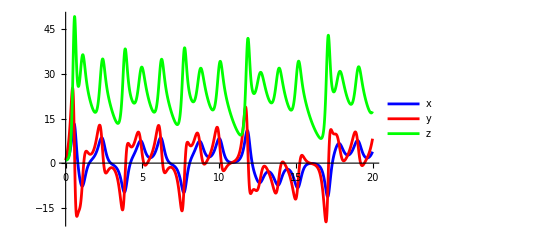

-Graphics3D-

```mathematica
Clear["Global`*"]
f1[y1_,y2_,y3_]:=3 (y2-y1);
f2[y1_,y2_,y3_]:=-y1*y3+27*y1-y2;
f3[y1_,y2_,y3_]:=y1*y2-y3;


a=0;
b=20;
h=0.01;
n=(b-a)/h;

t=Table[0,{i,1,IntegerPart[n]}];
y1=Table[1,{i,1,IntegerPart[n]}];
y2=Table[1,{i,1,IntegerPart[n]}];
y3=Table[1,{i,1,IntegerPart[n]}];


For[i=1,i<IntegerPart[n],i++,t[[i+1]]=t[[i]]+h;
y1[[i+1]]=y1[[i]]+h*f1[y1[[i]],y2[[i]],y3[[i]]];
y2[[i+1]]=y2[[i]]+h*f2[y1[[i]],y2[[i]],y3[[i]]];
y3[[i+1]]=y3[[i]]+h*f3[y1[[i]],y2[[i]],y3[[i]]];]

ListLinePlot[{Transpose[{t,y1}],Transpose[{t,y2}],Transpose[{t,y3}]},PlotStyle->{Blue,Red,Green},PlotRange->All,PlotLegends->{"x","y","z"}]

ListPointPlot3D[{Table[{y1[[i]],y2[[i]],y3[[i]]},{i,Length[t]}]},PlotStyle->{Blue,Red,Green},PlotRange->All,AxesLabel->{"y1","y2","y3"}]
```

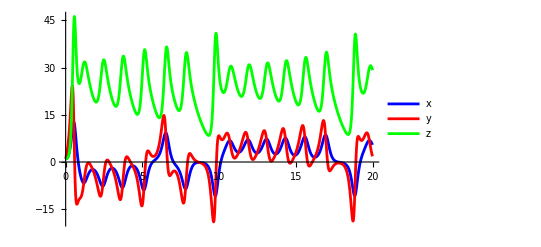

-Graphics3D-

```mathematica
f1[y1_,y2_,y3_]:=3 (y2-y1);
f2[y1_,y2_,y3_]:=-y1*y3+27*y1-y2;
f3[y1_,y2_,y3_]:=y1*y2-y3;

a=0;
b=20;
h=0.01;
n=(b-a)/h;

t=Table[0,{i,1,IntegerPart[n]}];
y1=Table[1,{i,1,IntegerPart[n]}];
y2=Table[1,{i,1,IntegerPart[n]}];
y3=Table[1,{i,1,IntegerPart[n]}];

For[i=1,i<IntegerPart[n],i++,t[[i+1]]=t[[i]]+h;
k1=h*f1[y1[[i]],y2[[i]],y3[[i]]];
l1=h*f2[y1[[i]],y2[[i]],y3[[i]]];
m1=h*f3[y1[[i]],y2[[i]],y3[[i]]];
k2=h*f1[y1[[i]]+k1/2,y2[[i]]+l1/2,y3[[i]]+m1/2];
l2=h*f2[y1[[i]]+k1/2,y2[[i]]+l1/2,y3[[i]]+m1/2];
m2=h*f3[y1[[i]]+k1/2,y2[[i]]+l1/2,y3[[i]]+m1/2];
k3=h*f1[y1[[i]]+k2/2,y2[[i]]+l2/2,y3[[i]]+m2/2];
l3=h*f2[y1[[i]]+k2/2,y2[[i]]+l2/2,y3[[i]]+m2/2];
m3=h*f3[y1[[i]]+k2/2,y2[[i]]+l2/2,y3[[i]]+m2/2];
k4=h*f1[y1[[i]]+k3,y2[[i]]+l3,y3[[i]]+m3];
l4=h*f2[y1[[i]]+k3,y2[[i]]+l3,y3[[i]]+m3];
m4=h*f3[y1[[i]]+k3,y2[[i]]+l3,y3[[i]]+m3];
y1[[i+1]]=y1[[i]]+(k1+2 k2+2 k3+k4)/6;
y2[[i+1]]=y2[[i]]+(l1+2 l2+2 l3+l4)/6;
y3[[i+1]]=y3[[i]]+(m1+2 m2+2 m3+m4)/6;]

ListLinePlot[{Transpose[{t,y1}],Transpose[{t,y2}],Transpose[{t,y3}]},PlotStyle->{Blue,Red,Green},PlotRange->All,PlotLegends->{"x","y","z"}]

ListPointPlot3D[{Table[{y1[[i]],y2[[i]],y3[[i]]},{i,Length[t]}]},PlotStyle->{Blue,Red,Green},PlotRange->All,AxesLabel->{"y1","y2","y3"}]
```

```mathematica
ClearAll["Global`*"]
```

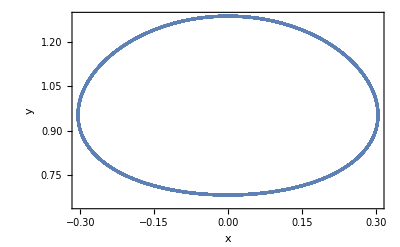

```mathematica
function[{x_,y_}]:={1 - x*x -y*y,2*x*y};

(*Метод Рунге-Кутты 4-го порядка*)
findResultRoungeHotta4toX[Y_,h_]:=Module[{k1,k2,k3,k4},k1=function[Y];
k2=function[Y+0.5*h*k1];
k3=function[Y+0.5*h*k2];
k4=function[Y+h*k3];
Y+h/6*(k1+2*k2+2*k3+k4)]

findSystem3ResultRoungeHotta4[startY_]:=Module[{h,Y,newY,n},h=0.01;
Y={startY};
n=IntegerPart[(lastdot-firstdot)/h];
Do[newY=findResultRoungeHotta4toX[Y[[-1]],h];
AppendTo[Y,newY],{i,1,n}];
Y]


firstdot=0;
lastdot=100;
EPS=0.2;


stY={0 - EPS,1 + EPS};


arr=findSystem3ResultRoungeHotta4[stY];


ListLinePlot[arr,PlotRange->All,Frame->True,FrameLabel->{"x","y"}]
```

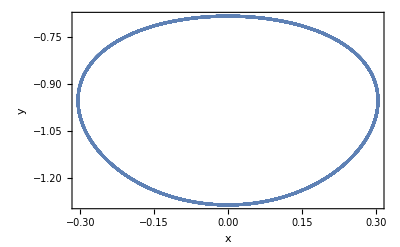

```mathematica
firstdot=0;
lastdot=100;
EPS=0.2;


stY={0 - EPS,-1 - EPS};


arr=findSystem3ResultRoungeHotta4[stY];


ListLinePlot[arr,PlotRange->All,Frame->True,FrameLabel->{"x","y"}]
```

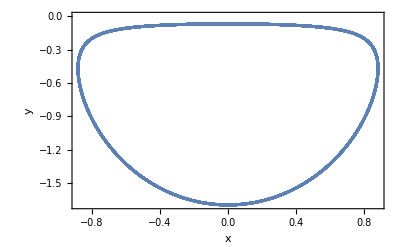

```mathematica
firstdot=0;
lastdot=100;
EPS=0.2;


stY={1 - EPS,0 - EPS};


arr=findSystem3ResultRoungeHotta4[stY];


ListLinePlot[arr,PlotRange->All,Frame->True,FrameLabel->{"x","y"}]
```

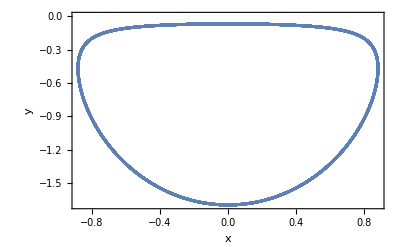

```mathematica
firstdot=0;
lastdot=100;
EPS=0.2;


stY={-1 + EPS,0 - EPS};


arr=findSystem3ResultRoungeHotta4[stY];


ListLinePlot[arr,PlotRange->All,Frame->True,FrameLabel->{"x","y"}]
```

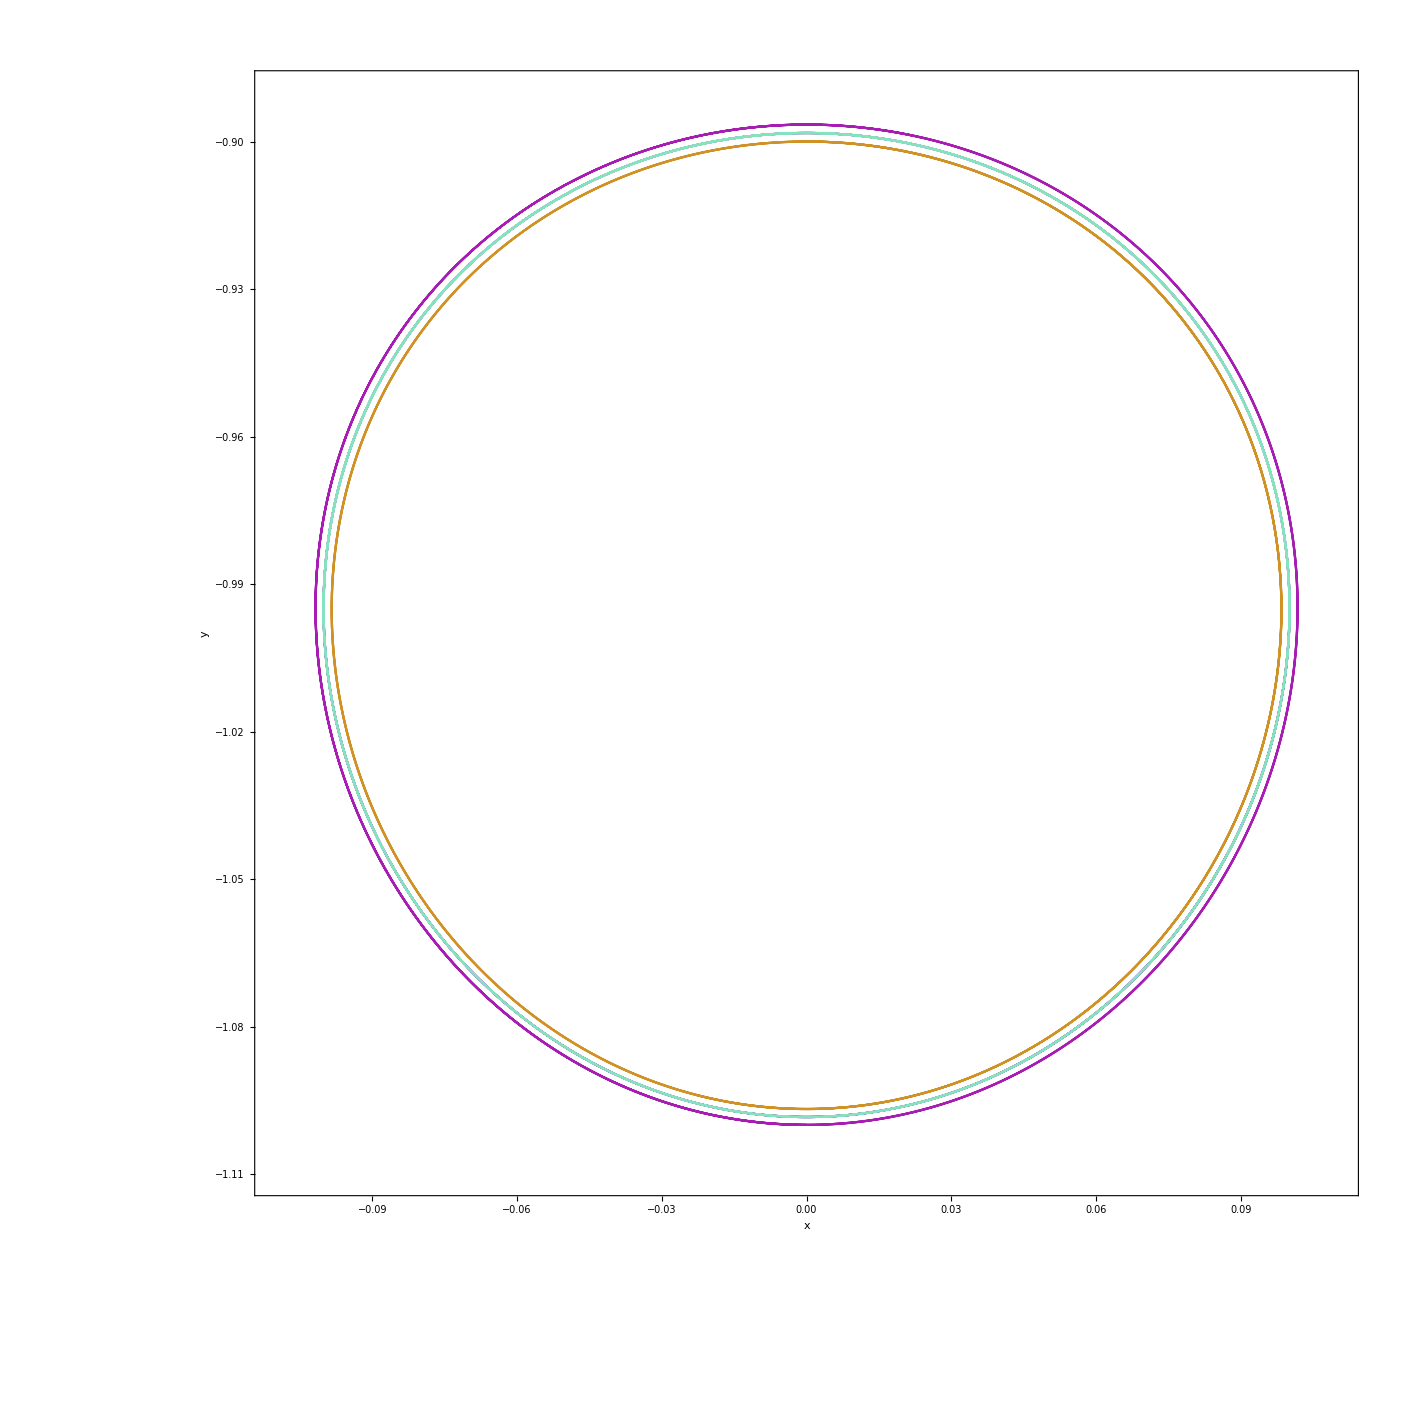

```mathematica
function[{x_,y_}]:={1-x^2-y^2,2 x y};

(*Метод Рунге-Кутты 4-го порядка*)
rungeKutta4[Y_,h_]:=Module[{k1,k2,k3,k4},k1=function[Y];
k2=function[Y+0.5 h k1];
k3=function[Y+0.5 h k2];
k4=function[Y+h k3];
Y+h/6 (k1+2 k2+2 k3+k4)];

(*Функция для нахождения решения системы методом Рунге-Кутты*)
findSystemResultRoungeHotta4[startY_,steps_,h_]:=NestWhileList[rungeKutta4[#,h]&,startY,Function[{y},Norm[y]<10],1,steps];

(*Найденные стационарные точки*)
equilibriumPoints={{0,-1},{0,1},{-1,0},{1,0}};

h=0.001;
steps=10000;
eps=0.1;

initialConditions=Flatten[Table[{equilibriumPoints[[i]]+{eps,0},
equilibriumPoints[[i]]+{0,eps},
equilibriumPoints[[i]]-{eps,0},
equilibriumPoints[[i]]-{0,eps}},
{i,Length[equilibriumPoints]}],1];


trajectories=Table[findSystemResultRoungeHotta4[initialConditions[[i]],steps,h],{i,Length[initialConditions]}];


Show[Table[ListLinePlot[trajectories[[i]],PlotRange->{{-1.1eps,1.1 eps},{-1 - 1.1 eps,-1 + 1.1 eps}}, AspectRatio -> 1,Frame->True,FrameLabel->{"x","y"},PlotStyle->RandomColor[]],{i,4}]]
```

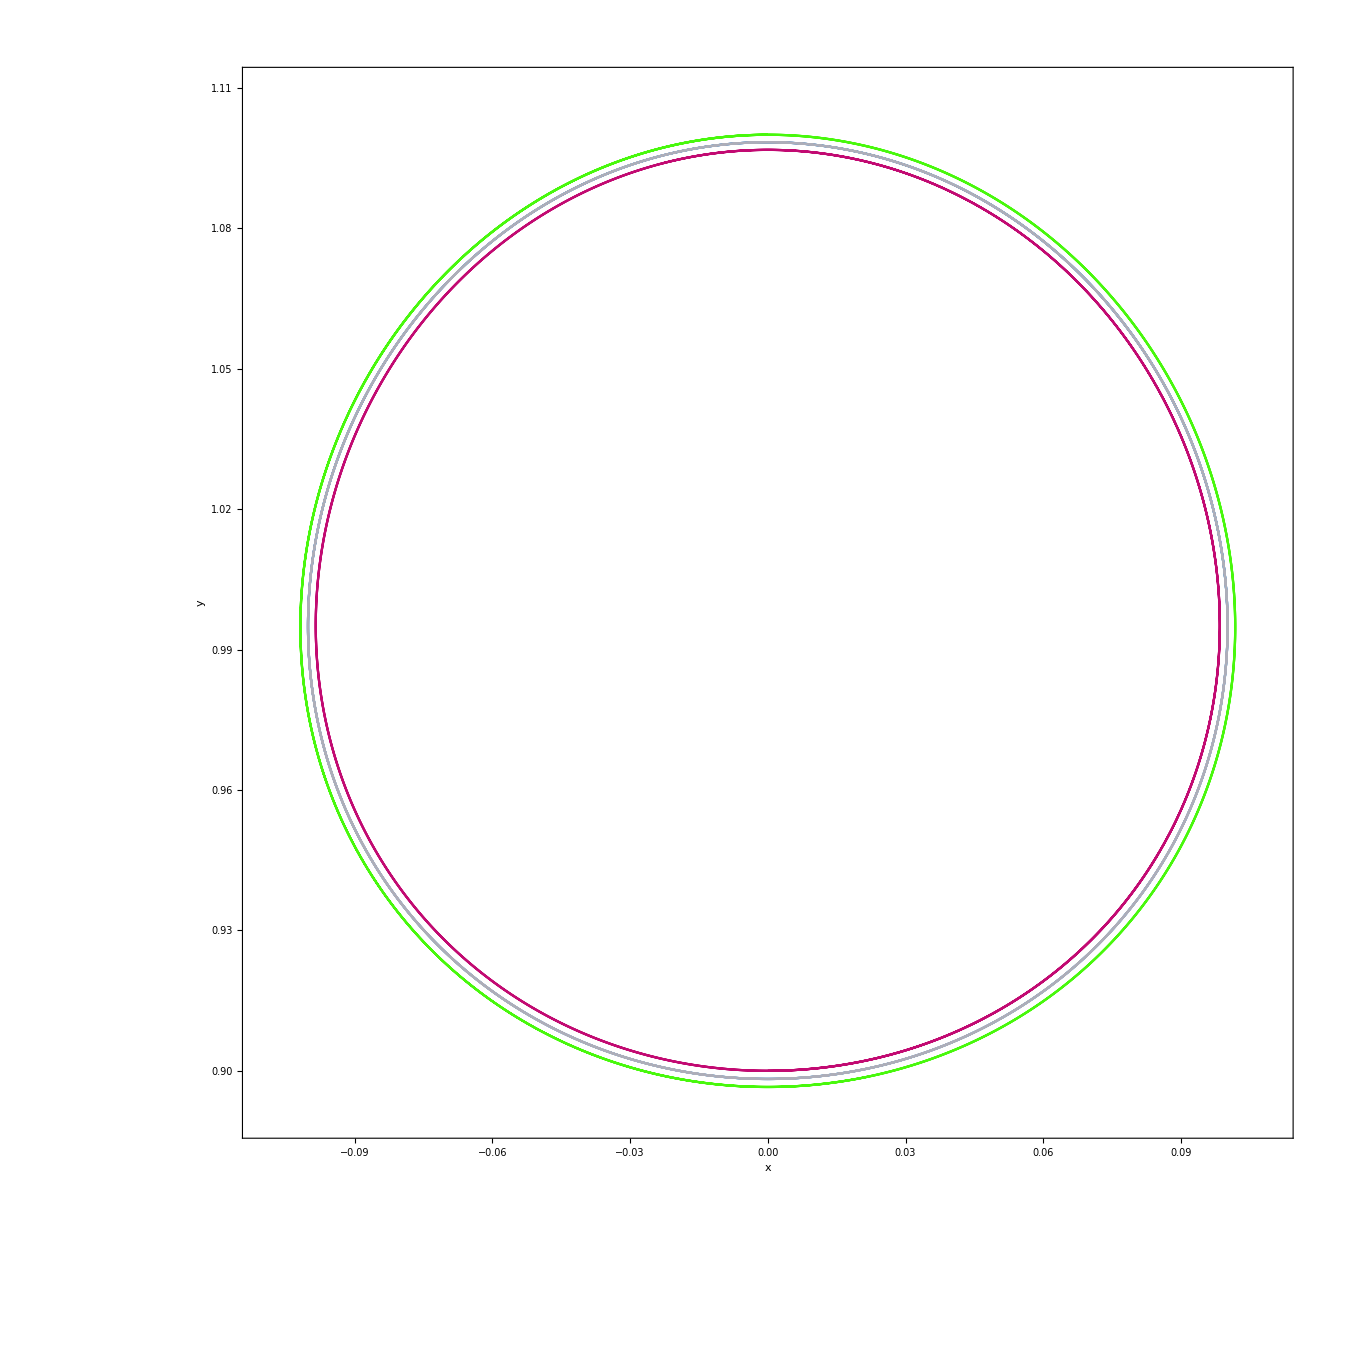

```mathematica
Show[Table[ListLinePlot[trajectories[[i]],PlotRange->{{-1.1eps,1.1 eps},{1 - 1.1 eps,1 + 1.1 eps}}, AspectRatio -> 1,Frame->True,FrameLabel->{"x","y"},PlotStyle->RandomColor[]],{i,5, 9}]]
```

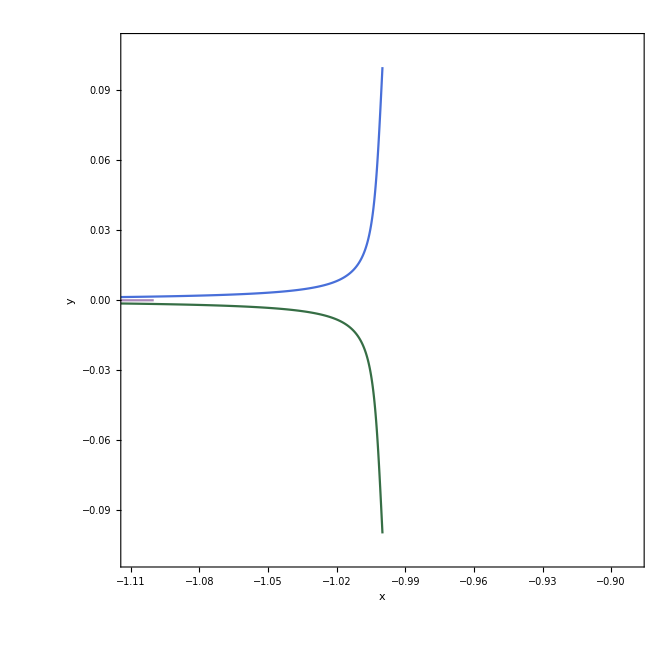

```mathematica
Show[Table[ListLinePlot[trajectories[[i]],PlotRange->{{-1 -1.1eps,-1 +1.1 eps},{-1.1 eps,1.1 eps}}, AspectRatio -> 1,Frame->True,FrameLabel->{"x","y"},PlotStyle->RandomColor[]],{i,10, 13}]]
```

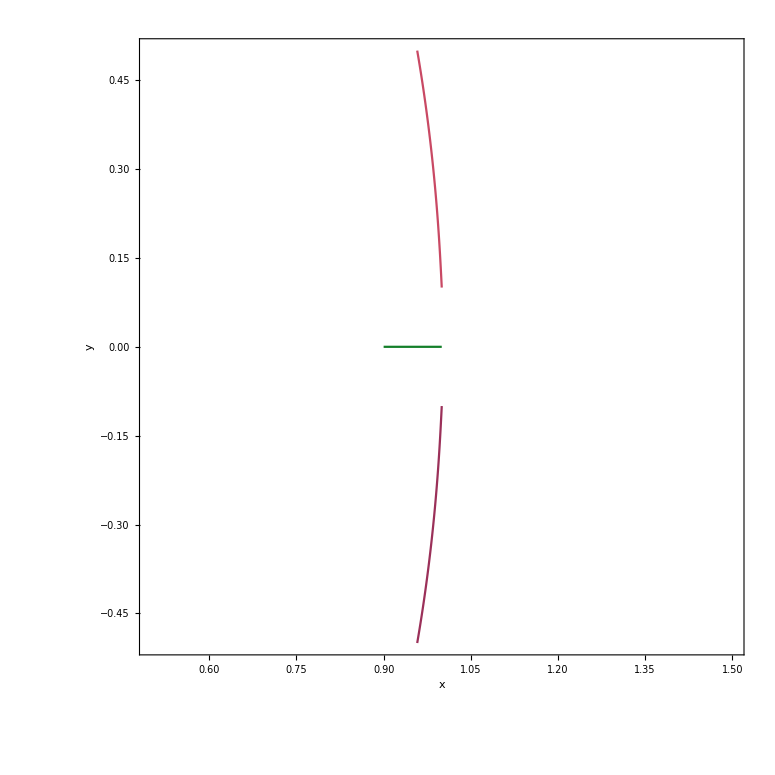

```mathematica
Show[Table[ListLinePlot[trajectories[[i]],PlotRange->{{1 -5eps,1 +5 eps},{-5 eps,5 eps}}, AspectRatio -> 1,Frame->True,FrameLabel->{"x","y"},PlotStyle->RandomColor[]],{i,14, 16}]]
```

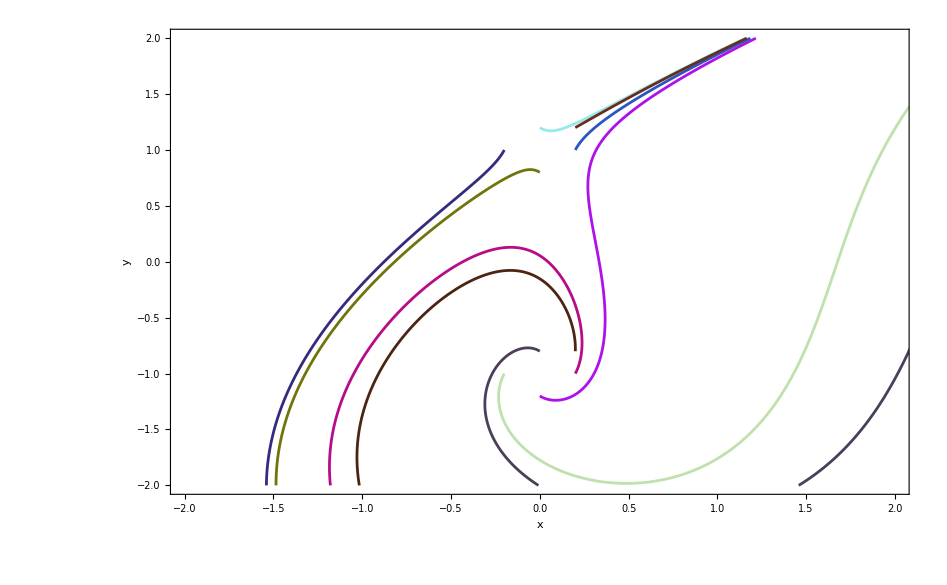

```mathematica
function[{x_,y_}]:={2*x+y^2-1,6*x-y^2+1};


rungeKutta4[Y_,t_]:=Module[{k1,k2,k3,k4},k1=function[Y];
k2=function[Y+0.5 h k1];
k3=function[Y+0.5 h k2];
k4=function[Y+h k3];
Y+t/6 (k1+2 k2+2 k3+k4)];

findSystemResultRoungeHotta4[startY_,steps_,t_]:=NestWhileList[rungeKutta4[#,t]&,
startY,Function[{y},Norm[y]<10],
1,steps];

equilibriumPoints={{0,-1},{0,1}};


h=0.001;
steps=20000;
eps=0.2;

(*Генерация начальных условий близких к стационарным точкам*)
initialConditions=Flatten[Table[{equilibriumPoints[[i]]+{eps,0},equilibriumPoints[[i]]+{0,eps},equilibriumPoints[[i]]-{eps,0},equilibriumPoints[[i]]-{0,eps}, equilibriumPoints[[i]]+{eps,eps}},{i,Length[equilibriumPoints]}],1];

(*Построение фазовых траекторий*)
trajectories=Table[findSystemResultRoungeHotta4[initialConditions[[i]],steps,h],{i,Length[initialConditions]}];


Show[Table[ListLinePlot[trajectories[[i]],PlotRange->{{-2,2},{-2,2}},Frame->True,FrameLabel->{"x","y"},PlotStyle->RandomColor[]],{i,Length[trajectories]}]]
```

2x+y^2-1==0 and 6x-y^2+1=0

WolframAlphaQueryResults